```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/plotting_routines

```mathematica
colorlist={Blue,Red,Darker[Green],Darker[Yellow],Orange,Purple,Cyan}
```

{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[Rational[2, 3], Rational[2, 3], 0],RGBColor[1, 0.5, 0],RGBColor[0.5, 0, 0.5],RGBColor[0, 1, 1]}

## Importing data

```mathematica
(*observed error, flag == 0,
 error grid, flag == 1 and 
error velocity flag == 2
num sol flag == 3
adjoint sol == 4,
fe_index = 5,
convergence_table_adaptive = 6*)
importdata[cycle_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/error_observed_cycle",ToString[cycle],".txt"],
flag == 1,
filename=StringJoin["../",outputdir,"/error_grid_cycle",ToString[cycle],".txt"],

flag == 2,
filename=StringJoin["../",outputdir,"/error_velocity_cycle",ToString[cycle],".txt"],
flag == 3,
filename=StringJoin["../",outputdir,"/result_cycle",ToString[cycle],".txt"],
flag == 4,
filename=StringJoin["../",outputdir,"/resultAdj_cycle",ToString[cycle],".txt"],
flag == 5,
filename=StringJoin["../",outputdir,"/fe_index_cycle",ToString[cycle],".txt"],
flag == 6,
filename=StringJoin["../",outputdir,"/convergence_table_adaptive",".txt"];
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]
]

SortData[data_]:=Module[{indices},
indices = Ordering[data⟦All,1⟧,All,GreaterEqual];
data⟦indices,All⟧
]
```

## Validation of error prediction

### Plotting Routine

#### Routines for Grid

```mathematica
CreateConvergencePlot[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
PredictedError=Table[0,{ii,1,Length[Mvalues]}];
Do[PredictedError⟦ii⟧ = Abs[data[Mvalues⟦ii⟧]⟦All,{6,9}⟧],{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black},{Dashed,Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];
PredictedError=Insert[PredictedError,ExactOrder[500,2000,10^-3,-1],-1];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"True Error"},{"Reference Order"}}];

ListLogLogPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,10},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Error In Target Functional",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]

CreateEfficiencyIndexPlot[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
PredictedError=Table[0,{ii,1,Length[Mvalues]}];
Do[PredictedError⟦ii⟧ = Abs[data[Mvalues⟦ii⟧]⟦All,{6,9}⟧],{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];

Do[PredictedError⟦ii⟧⟦All,2⟧=TrueError⟦All,2⟧/PredictedError⟦ii⟧⟦All,2⟧,{ii,1,Length[PredictedError]}];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"Desired Value"},}];

ListPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,10},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Efficiency Index",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]
ExactOrder[x1_,x2_,y1_,order_]:={{x1,y1},{x2,y1*Exp[order*Log[x2/x1]]}};
```

#### Routines for Velocity Space

```mathematica
CreateEfficiencyIndexPlotVelocity[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
TrueError⟦All,2⟧ = Table[1,{ii,1,Length[TrueError]}]*(BoundaryTargetPoisson[40]-BoundaryTargetPoisson[6]);

PredictedError=Table[0,{ii,1,Length[Mvalues]}];
Do[PredictedError⟦ii⟧ = Abs[data[Mvalues⟦ii⟧]⟦All,{6,11}⟧],{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];

Do[PredictedError⟦ii⟧⟦All,2⟧=TrueError⟦All,2⟧/PredictedError⟦ii⟧⟦All,2⟧,{ii,1,Length[PredictedError]}];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"Desired Value"},}];

ListPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,12},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Efficiency Index",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]

CreateConvergencePlotVelocity[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
TrueError⟦All,2⟧ = Table[1,{ii,1,Length[TrueError]}]*(BoundaryTargetPoisson[40]-BoundaryTargetPoisson[6]);

PredictedError=Table[0,{ii,1,Length[Mvalues]}];
Do[PredictedError⟦ii⟧ = Abs[data[Mvalues⟦ii⟧]⟦All,{6,11}⟧],{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"True Error"}}];

ListLogLogPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,12},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Error In Target Functional",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]
```

#### Routines for Total Error

```mathematica
CreateConvergencePlotTotal[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
PredictedError=Table[0,{ii,1,Length[Mvalues]}];

Do[PredictedError⟦ii⟧ = data[Mvalues⟦ii⟧]⟦All,{6,9}⟧;
PredictedError⟦ii⟧⟦All,2⟧+=data[Mvalues⟦ii⟧]⟦All,11⟧;
PredictedError⟦ii⟧=Abs[PredictedError⟦ii⟧];,{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"True Error"}}];

ListLogLogPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,10},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Error In Target Functional",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]

CreateEfficiencyIndexPlotTotal[data_,Mvalues_]:=Module[{PredictedError,TrueError,legends,plotStyle,exactLine},

TrueError = Abs[data[Mvalues⟦1⟧]⟦All,{6,7}⟧];
PredictedError=Table[0,{ii,1,Length[Mvalues]}];

Do[PredictedError⟦ii⟧ = data[Mvalues⟦ii⟧]⟦All,{6,9}⟧;
PredictedError⟦ii⟧⟦All,2⟧+=data[Mvalues⟦ii⟧]⟦All,11⟧;
PredictedError⟦ii⟧=Abs[PredictedError⟦ii⟧];,{ii,1,Length[Mvalues]}];

plotStyle = Join[Table[If[EvenQ[Mvalues⟦ii⟧],{colorlist⟦ii⟧},{Dashed,colorlist⟦ii⟧}],{ii,1,Length[Mvalues]}],{{Thickness[0.005],Black}}];

(*insert the true error*)
PredictedError = Insert[PredictedError,TrueError,-1];
Do[PredictedError⟦ii⟧⟦All,2⟧=TrueError⟦All,2⟧/PredictedError⟦ii⟧⟦All,2⟧,{ii,1,Length[PredictedError]}];

legends = Flatten[{Table[StringJoin["M=",ToString[ii]],{ii,Mvalues}],{"Desired Value"}}];

ListLogLogPlot[PredictedError,Joined->True,PlotMarkers->{Automatic,10},PlotLegends->legends,ImageSize->800,GridLines->Automatic,Frame->True,FrameLabel->{{Style["Efficiency Index",FontSize->16],None},{Style["number of dofs",FontSize->16],None}},FrameTicksStyle->Directive[Black,14],PlotStyle->plotStyle]
]
ExactOrder[x1_,x2_,y1_,order_]:={{x1,y1},{x2,y1*Exp[order*Log[x2/x1]]}};
```

### grid error

```mathematica
baseFile = "2x1v_moments_wall_Adp/validate_grid_error";
MvaluesGrid = {6,7,8,9,10,11,12};
```

```mathematica
Do[filename = StringJoin[baseFile,"/M",ToString[ii]];
tableGrid[ii]=importdata[0,6,filename]⟦2;;-1,All⟧;,{ii,MvaluesGrid}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M6/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M7/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M8/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M9/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M10/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M11/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_grid_error/M12/convergence_table_adaptive.txt

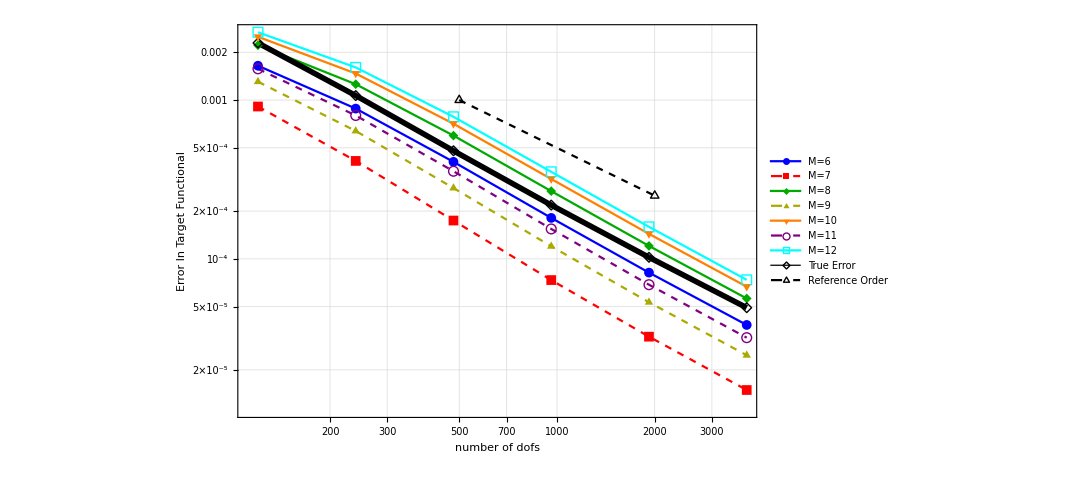

```mathematica
CreateConvergencePlot[tableGrid,MvaluesGrid]
```

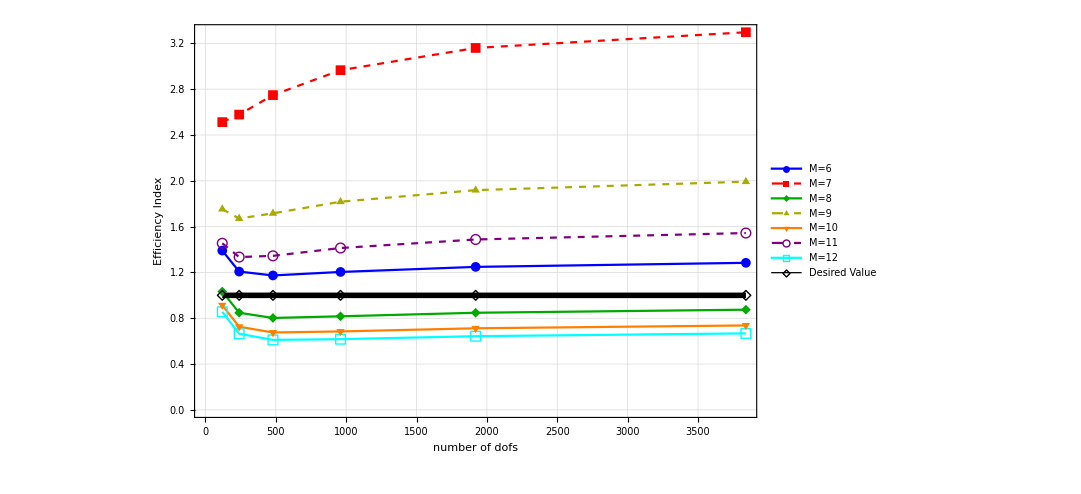

```mathematica
CreateEfficiencyIndexPlot[tableGrid,MvaluesGrid]
```

### Velocity error

```mathematica
baseFile = "2x1v_moments_wall_Adp/validate_velocity_error";
MvaluesVelocity = {7,8,9,10,11,12};
```

```mathematica
Do[filename = StringJoin[baseFile,"/M",ToString[ii]];
tableVelocity[ii]=importdata[0,6,filename]⟦2;;-1,All⟧;,{ii,MvaluesVelocity}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M7/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M8/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M9/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M10/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M11/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M12/convergence_table_adaptive.txt

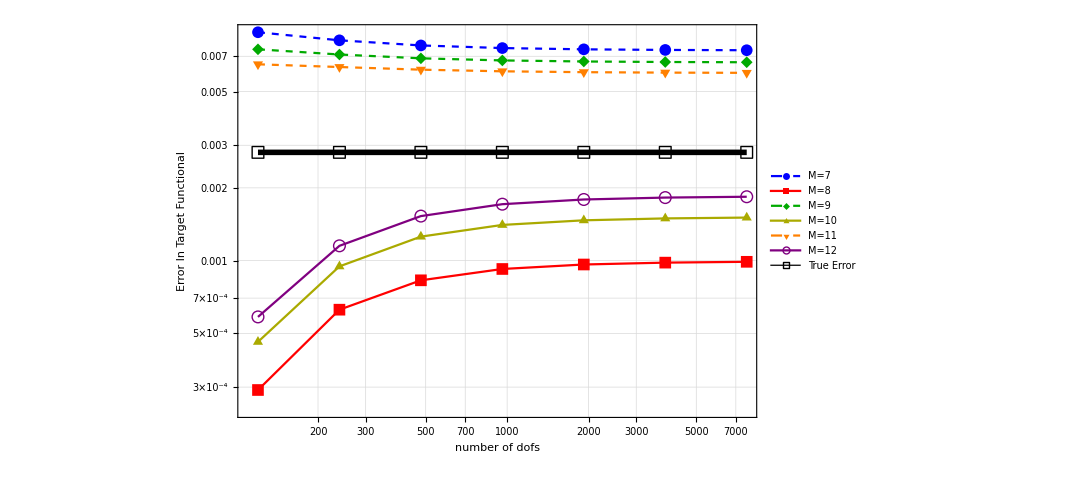

```mathematica
CreateConvergencePlotVelocity[tableVelocity,MvaluesVelocity]
```

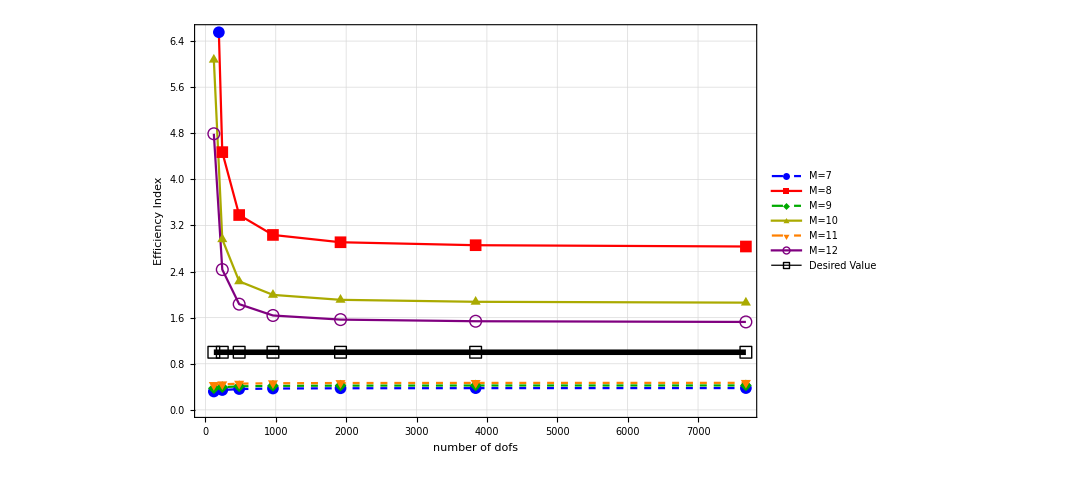

```mathematica
CreateEfficiencyIndexPlotVelocity[tableVelocity,MvaluesVelocity]
```

### Total Error

```mathematica
baseFile = "2x1v_moments_wall_Adp/validate_velocity_error";
MvaluesTotal = {7,8,9,10,11,12};
```

```mathematica
Do[filename = StringJoin[baseFile,"/M",ToString[ii]];
tableTotal[ii]=importdata[0,6,filename]⟦2;;-1,All⟧;,{ii,MvaluesTotal}];
```

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M7/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M8/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M9/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M10/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M11/convergence_table_adaptive.txt

Reading Data from...

../2x1v_moments_wall_Adp/validate_velocity_error/M12/convergence_table_adaptive.txt

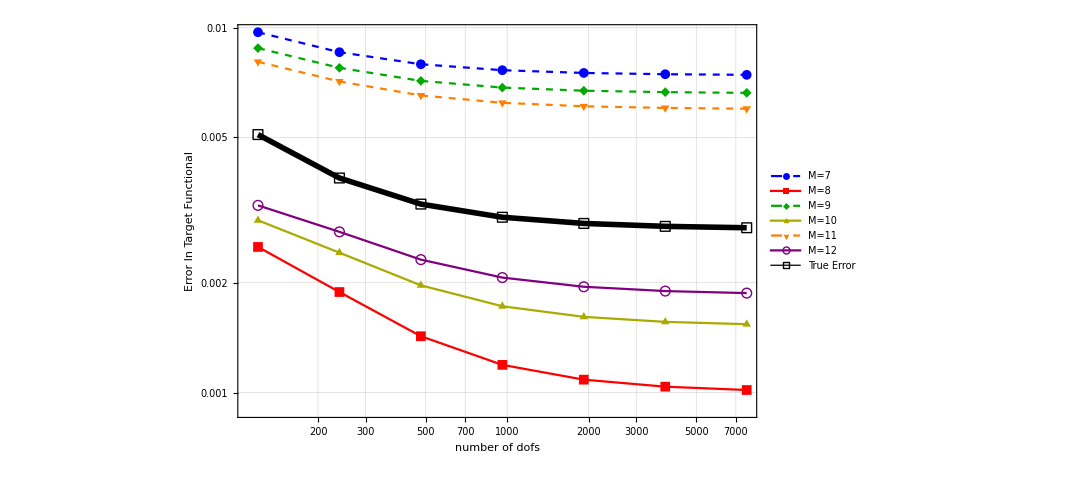

```mathematica
CreateConvergencePlotTotal[tableTotal,MvaluesTotal]
```

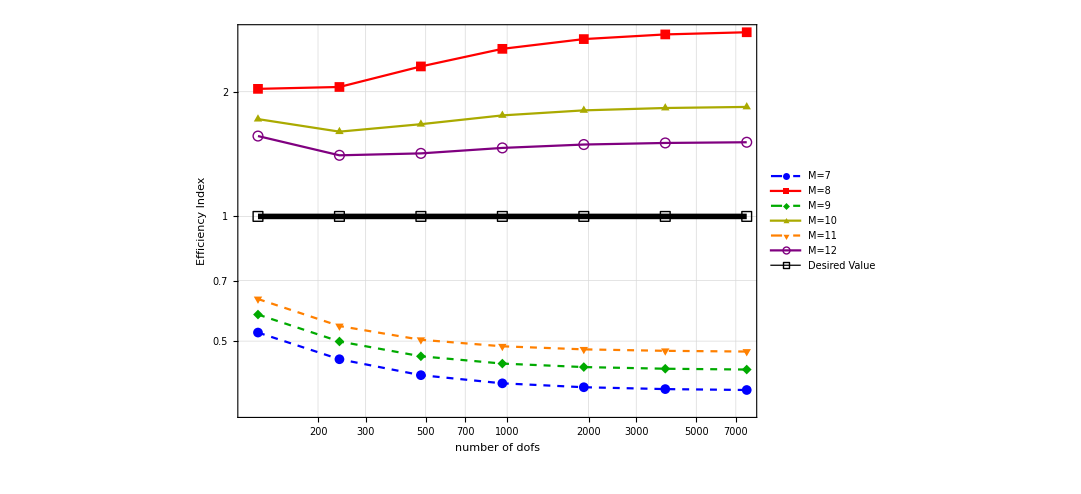

```mathematica
CreateEfficiencyIndexPlotTotal[tableTotal,MvaluesTotal]
```

## Convergence Rates Comparison

```mathematica
convgAdpGamma3 = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive_gamma_3.txt","Table"];
convgAdpGamma2 = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive_gamma_2.txt","Table"];
convgAdpGamma0p5 = Import["../2x1v_moments_wall_Adp/convergence_table_adaptive_gamma_0p5.txt","Table"];
convgUni = Import["../2x1v_moments_wall_Adp/convergence_table_uniform.txt","Table"];
```

### Plotting Routine

```mathematica
CompareConvergence[dataAdp_,dataUni_]:=Module[{IDdofs,IDError,IDCorrected,IDPredicted},

IDdofs = 6;
IDError = 7;
IDCorrected=11;
IDPredicted = -1;

ListLogLogPlot[{dataUni⟦2;;-1,{IDdofs,IDError}⟧,dataAdp⟦2;;-1,{IDdofs,IDError}⟧,dataAdp⟦2;;-1,{IDdofs,IDPredicted}⟧(*,dataAdp⟦2;;-1,{IDdofs,IDCorrected}⟧*)},Joined->True,PlotLegends->{"Uniform","Adjoint","Predicted"(*,"Adjoint Corrected"*)},PlotMarkers->{Automatic,14},ImageSize->Large,PlotRange->Full,Frame->True,
FrameLabel->{{Style["Error in Target Functional",FontSize->16],None},{Style["Number Of Dofs",FontSize->16],None}},ImageSize->800,GridLines->Automatic,FrameTicksStyle->Directive[Black,14],PlotStyle->{Black,Red,Green,Magenta}]
]
```

```mathematica
PlotCorrectedValue[dataAdp_,dataUni_]:=Module[{IDdofs,IDError,IDCorrected,IDPredicted},

IDdofs = 6;
IDError = 7;
IDCorrected=11;

ListLogLogPlot[{dataUni⟦2;;-1,{IDdofs,IDError}⟧,dataAdp⟦2;;-1,{IDdofs,IDCorrected}⟧},Joined->True,PlotLegends->{"Uniform","Adjoint Corrected"},PlotMarkers->{Automatic,14},ImageSize->Large,PlotRange->Full,Frame->True,
FrameLabel->{{Style["Error in Target Functional",FontSize->16],None},{Style["Number Of Dofs",FontSize->16],None}},ImageSize->800,GridLines->Automatic,FrameTicksStyle->Directive[Black,14],PlotStyle->{Black,Magenta}]
]
```

```mathematica
CompareConvergence2[dataAdp_,dataUni_]:=Module[{IDdofs,IDError,IDCorrected,IDPredicted},

IDdofs = 1;
IDError = 2;
IDPredicted = 3;

ListLogLogPlot[{Abs[dataUni⟦2;;-1,{6,7}⟧],Abs[dataAdp⟦2;;-1,{IDdofs,IDError}⟧],Abs[dataAdp⟦2;;-1,{IDdofs,IDPredicted}⟧](*,dataAdp⟦2;;-1,{IDdofs,IDPredicted}⟧*)},Joined->True,PlotLegends->{"Uniform","Adjoint","Predicted"(*,"Adjoint Corrected"*)},PlotMarkers->{Automatic,14},ImageSize->Large,PlotRange->Full,Frame->True,
FrameLabel->{{Style["Error in Target Functional",FontSize->16],None},{Style["Number Of Dofs",FontSize->16],None}},ImageSize->800,GridLines->Automatic,FrameTicksStyle->Directive[Black,14],PlotStyle->{Black,Red,Green,Magenta}]
]
```

### Results

#### compare convergence

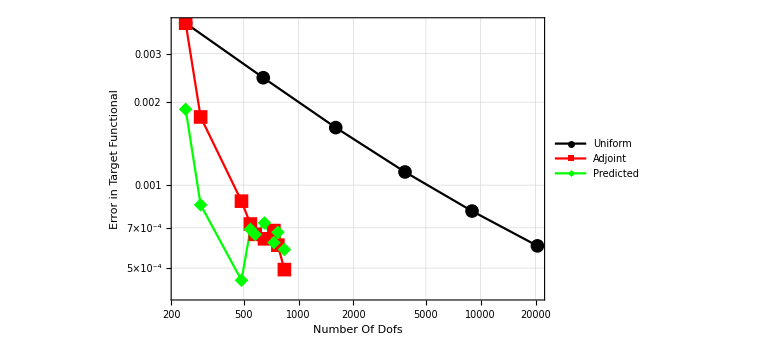

```mathematica
CompareConvergence[convgAdpGamma3⟦Flatten[Join[{Range[1,3,1],Range[7,13]}]],All⟧,convgUni]
```

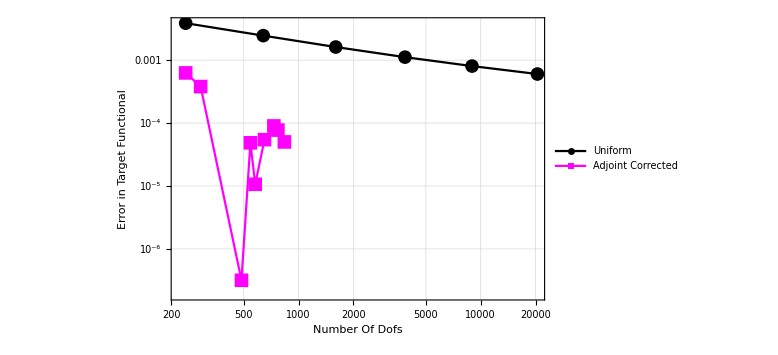

```mathematica
PlotCorrectedValue[convgAdpGamma3⟦Flatten[Join[{Range[1,3,1],Range[7,13]}]],All⟧,convgUni]
```

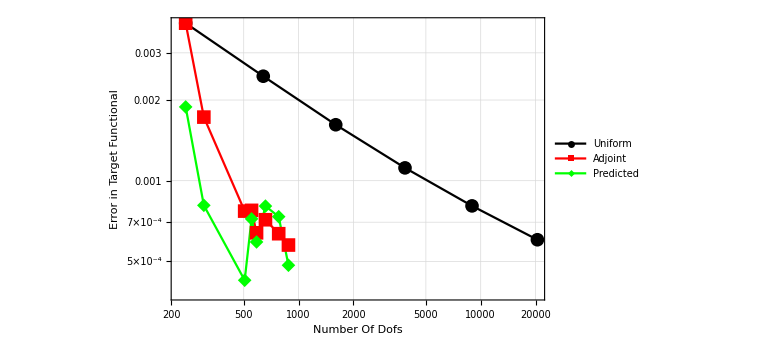

```mathematica
CompareConvergence2[convgAdpGamma2⟦Flatten[Join[{Range[1,3,1],Range[7,12]}]],All⟧,convgUni]
```

#### h-m grid

```mathematica
Mvariation = Import["../2x1v_moments_wall_Adp/fe_index_gamma_3_cycle5.txt","Table"];
```

```mathematica
Mvariation12 = Mvariation⟦Flatten[Position[Mvariation⟦All,4⟧,12]],{1,4}⟧;
Mvariation10 = Mvariation⟦Flatten[Position[Mvariation⟦All,4⟧,10]],{1,4}⟧;
Mvariation6 = Mvariation⟦Flatten[Position[Mvariation⟦All,4⟧,6]],{1,4}⟧;
Mvariation8 = Mvariation⟦Flatten[Position[Mvariation⟦All,4⟧,8]],{1,4}⟧;
```

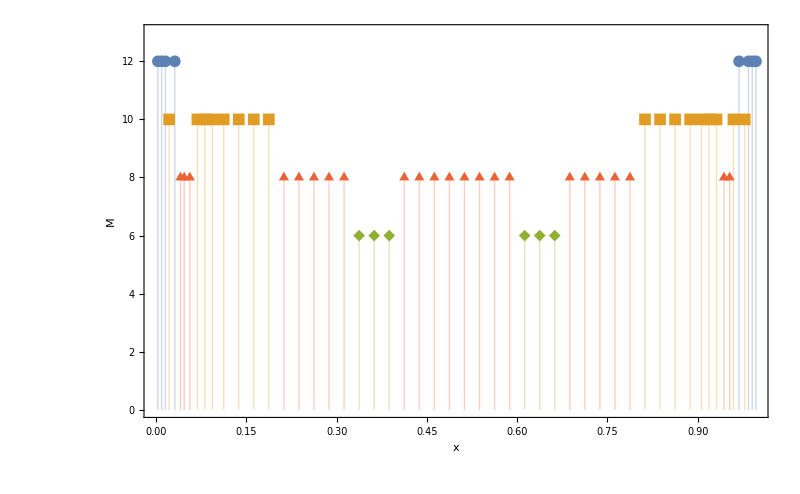

```mathematica
ListPlot[{Mvariation12,Mvariation10,Mvariation6,Mvariation8},Frame->True,Filling->Axis,PlotRange->{Full,{0,13}},ImageSize->800,FrameTicksStyle->Directive[Black,14],PlotMarkers->{Automatic,12},
FrameLabel->{{Style["M",FontSize->16],None},{Style["x",FontSize->16],None}},RotateLabel->False]
```

#### grid and velocity error comparison

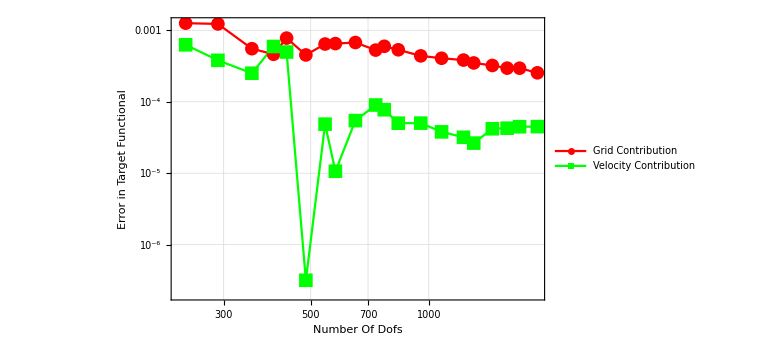

```mathematica
ListLogLogPlot[{Abs[convgAdpGamma3⟦2;;-1,{6,9}⟧],Abs[convgAdpGamma3⟦2;;-1,{6,11}⟧]},Joined->True,PlotLegends->{"Grid Contribution","Velocity Contribution"},PlotMarkers->{Automatic,14},ImageSize->Large,PlotRange->Full,Frame->True,
FrameLabel->{{Style["Error in Target Functional",FontSize->16],None},{Style["Number Of Dofs",FontSize->16],None}},ImageSize->800,GridLines->Automatic,FrameTicksStyle->Directive[Black,14],PlotStyle->{Red,Green}]
```